```mathematica
2-2
```

0

```mathematica
Needs["GraphUtilities`"];
```

# Series/Parallel Reducability

Nicholas Wheeler
21 November 2011

### Introduction

My objective is to discover a criterion or algorithm by means of which one can discover by inspection whether or not a given circuit yields to series/paralled decomposition. I begin with no clear idea in mind…with some simple exploratory doodles, informed only by the hunch that the problem may be best approached by looking to patterns (if any) that emerge when uses series/parallel constructions to build up complex circuits; i.e., that assembly may be more informative than disassembly.

```mathematica
R[x_,y_]:=x->y
```

### Exploratory doodles

```mathematica
g={R[1,2],R[2,3],R[3,4],R[3,4],R[4,5],R[2,5],R[5,6]};
```

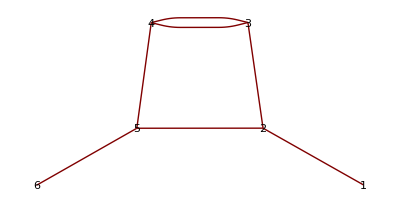

```mathematica
GraphPlot[g,VertexLabeling->True]
```

```mathematica
AdjacencyMatrix[g]//MatrixForm
```

(0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 2 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0)

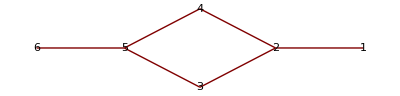

(0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Wheat={R[1,2],R[2,3],R[2,4],R[3,5],R[4,5],R[5,6]};
GraphPlot[Wheat,VertexLabeling->True]
AdjacencyMatrix[Wheat]//MatrixForm
```

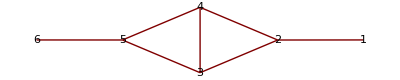

(0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0
0 | 0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Wheatstone={R[1,2],R[2,3],R[2,4],R[3,4],R[3,5],R[4,5],R[5,6]};
GraphPlot[Wheatstone,VertexLabeling->True]
AdjacencyMatrix[Wheatstone]//MatrixForm
```

```mathematica
𝕄=({{0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 1, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 1}, {0, 0, 0, 0, 0, 0, 0, 0}});
```

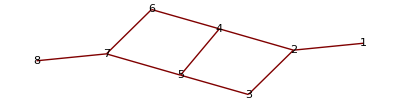

```mathematica
GraphPlot[𝕄,VertexLabeling->True]
```